## CellsOnBoundary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 12:19:36
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate a random template constrained to  circle of radius 100 with at least 50 cells.  The actual number of cells will be the smallest integer square larger than 50.

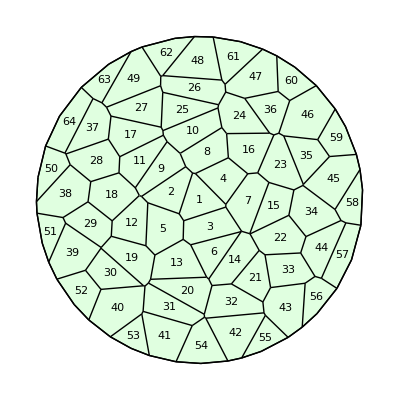

```mathematica
w=TemplateRandomCircularGrid[50,100];
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
n=NTissueCells[w]
```

64

Determine the cells that are on the "edge" of the tissue

```mathematica
cbw=CellsOnBoundary[w]
```

{38,39,40,41,42,43,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

Color the "boundary" cells a different color.

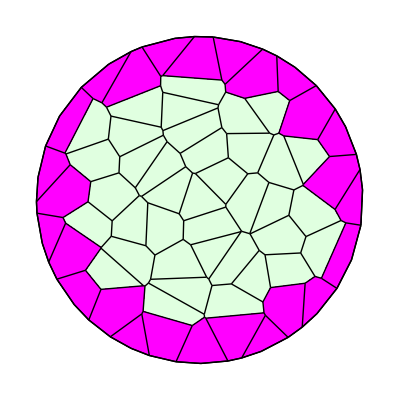

```mathematica
ShowTissueCells[w, cbw, Magenta]
```

It will also identify interior boundary cells, such as those around an ablated center:

```mathematica
u=RemoveCell[w, {1,2,3}];
nu=NTissueCells[u];
cbu=CellsOnBoundary[u];
```

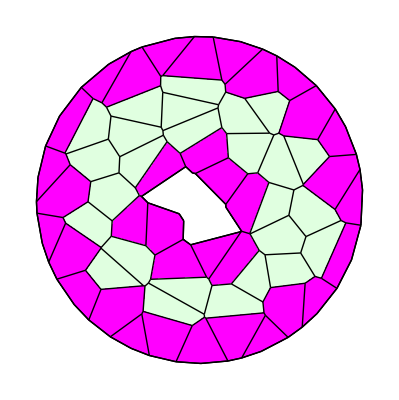

```mathematica
ShowTissueCells[u,cbu, Magenta]
```